# Modifying Lists

Math 213 - Math with Mathematica
Christopher Hanusa

## Aim

This tutorial first starts off with some shortcuts to make your life with Mathematica easier.  Then we develop tools for creating, accessing, and modifying lists.

Tip: You can evaluate ALL cells in this file in order using the Evaluation > Evaluate Notebook command.

## Defining variables using the = operator

It is often helpful to define the output of a command to be able to reuse it later.  To do this, use the = operator:

```mathematica
a=Range[3]
```

{1,2,3}

```mathematica
a
```

{1,2,3}

If you don’t want to see the output of a command, you can end the line with a semicolon.

```mathematica
a=Range[4];
```

```mathematica
a
```

{1,2,3,4}

Important: it matters the order in which you evaluate commands.  For example, if you re-evaluate the first instance of a, it will return its last-defined definition, which is {1,2,3,4}.

I HIGHLY suggest that you give descriptive names to your variables. Since all built-in Mathematica commands start with a captial letter, a nice convention to use for your own variable names is to start with a lowercase letter and if variable is multiple words long, capitalize the start of each new word.

```mathematica
iAmANewVariable=Range[Pi,2Pi,Pi/2]
```

```mathematica
heyYouWhatsThatSound=Play[Sin[440 2Pi t],{t,0,1}]
```

(OK, the provided example names aren’t very descriptive, but you get the idea....it’s #likeAHashtag.)

## Shortcut: the % operator

A useful but slightly dangerous operator is %, which stands for the most recent output.  So, for instance, if you decide to make a list, and then decide you want to create a scatterplot, you can do the following:

```mathematica
Table[RandomInteger[{1,3}],{100}]
```

{2,2,2,1,3,2,3,2,2,3,3,1,1,1,1,3,1,2,1,3,3,1,2,1,2,3,3,1,2,1,1,3,3,1,2,2,1,1,2,3,1,2,1,1,2,1,1,3,3,1,3,2,3,3,3,3,1,2,3,3,2,2,1,2,3,3,1,2,3,1,3,2,3,3,2,1,3,3,2,2,3,2,3,2,2,1,3,1,2,2,3,1,2,1,2,1,3,3,2,1}

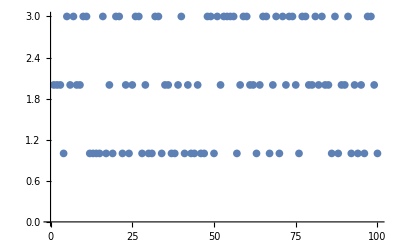

```mathematica
ListPlot[%]
```

The reason it is dangerous is related to the above discussion where the order in which you evaluate commands matters.  If you tried to re-evaluate the previous line of code, you would get an error, because you can’t create a scatterplot of a scatterplot!

```mathematica
ListPlot[%]
```

ListPlot::lpn: is not a list of numbers or pairs of numbers.

ListPlot[-Graphics-]

In the same vein is %% (for two outputs back); slightly more safe might be Out[n] to be explicit about wanting the nth output.  (But this will depend on the session in which you are working, so it would be different each time you re-open your notebook!!!!)  It is best to define a new variable when you think you will be using the output later.

## Postfix a command using //

So let’s say you have created a beautiful command such as

```mathematica
Table[Range[i,10],{i,1,10}]
```

{{1,2,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10},{4,5,6,7,8,9,10},{5,6,7,8,9,10},{6,7,8,9,10},{7,8,9,10},{8,9,10},{9,10},{10}}

And then suppose you are at the end of the line and are too lazy to go to the beginning of the line to display the table in a beautiful way like this:

```mathematica
TableForm[Table[Range[i,10],{i,1,10}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 |  | 
4 | 5 | 6 | 7 | 8 | 9 | 10 |  |  | 
5 | 6 | 7 | 8 | 9 | 10 |  |  |  | 
6 | 7 | 8 | 9 | 10 |  |  |  |  | 
7 | 8 | 9 | 10 |  |  |  |  |  | 
8 | 9 | 10 |  |  |  |  |  |  | 
9 | 10 |  |  |  |  |  |  |  | 
10 |  |  |  |  |  |  |  |  |

Instead, you are able to use the // operator which applies the command after // to the start of the expression, like this:

```mathematica
Table[Range[i,10],{i,1,10}] // TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 |  | 
4 | 5 | 6 | 7 | 8 | 9 | 10 |  |  | 
5 | 6 | 7 | 8 | 9 | 10 |  |  |  | 
6 | 7 | 8 | 9 | 10 |  |  |  |  | 
7 | 8 | 9 | 10 |  |  |  |  |  | 
8 | 9 | 10 |  |  |  |  |  |  | 
9 | 10 |  |  |  |  |  |  |  | 
10 |  |  |  |  |  |  |  |  |

## When you’ve gotten yourself in trouble

### When you don’t understand a command.

By now you should know that you can search in the Documentation Center when you want more information about a command.  You can get quick information about a command directly in a Mathematica notebook by using the ? operator.

```mathematica
?Tally
```

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities.
Tally[list,test] uses test to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

Notice the >> symbol at the end of the command information.  Click there to go directly to the Documentation Center.

### When you define something you shouldn’t have.

Suppose you define a variable at some point:

```mathematica
x=10
```

10

Perhaps later in your file you wanted to generate the list {x+1,x+2,x+3} using the Table command:

```mathematica
Table[x+i,{i,3}]
```

{11,12,13}

Since x had been defined before, the generated list has no x’s in it.  When you run into such a problem, you use the Remove command:

```mathematica
Remove[x];
Table[x+i,{i,3}]
```

{1+x,2+x,3+x}

### When your code won’t stop running

We all get into infinite loops sometimes or take on too much work.  To stop Mathematica in the middle of a calculation, use (Option-.) or (Ctrl-.)  (That’s a period!)  
Try it here after removing the (* and *) which I used to comment out the command.

```mathematica
(* For[i=0,i≥0,i++,i] *)
```

## Comprehension Questions:

### 1. Practice using the % operator. First, define and evaluate some list of even numbers by way of a Range or Table command. Then divide the list by 2 to divide each entry by 2. Then add 10 to the list. And then give a scatterplot of this final list.

### 2. Use the ? operator to learn about the commands First and Rest.

## The Table command, Part 2

### More Variables

The Table command can also create a list with two or more variables changing at a time.  Simply put two variable ranges as inputs.  In the following example, we consider all values of x from 1 to 3 and all values of y from 1 to 3 and multiply them together (because that's what the function x*y says to do).

```mathematica
Table[x*y,{x,3},{y,3}]
```

{{1,2,3},{2,4,6},{3,6,9}}

It is often a good idea to give the list of points you want to plot a descriptive name first.

### More Complicated Functions

The Table command is much more powerful than simply creating lists of numbers.  For instance, you can create lists of anything in the language of Mathematica:

Graphics objects:

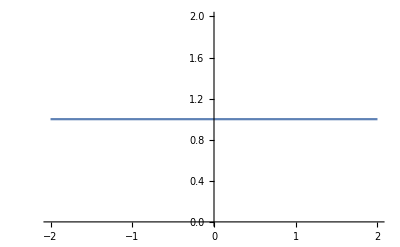
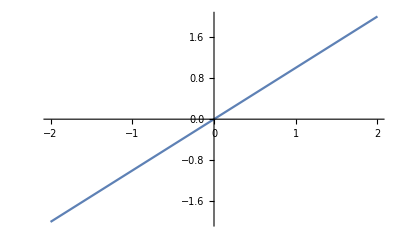

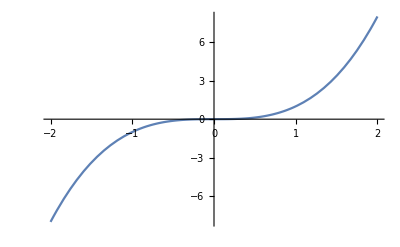
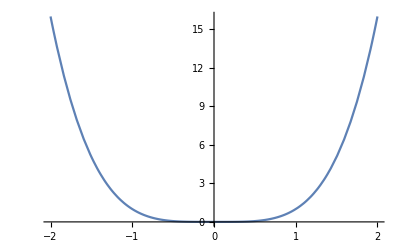
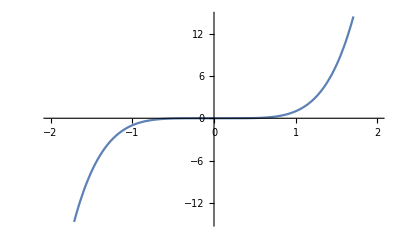
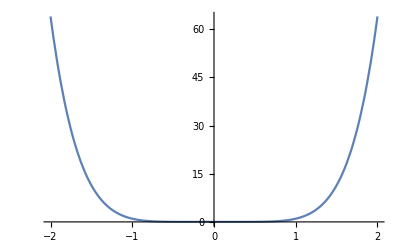
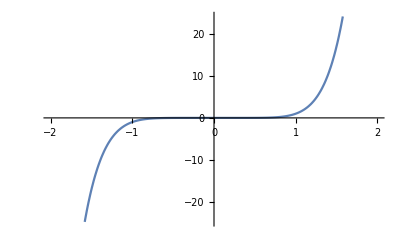
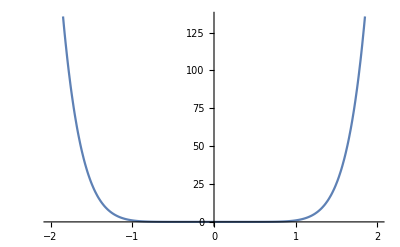

```mathematica
Table[Plot[x^n,{x,-2,2}],{n,0,10}]
```

Coordinates of a hexagon:

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

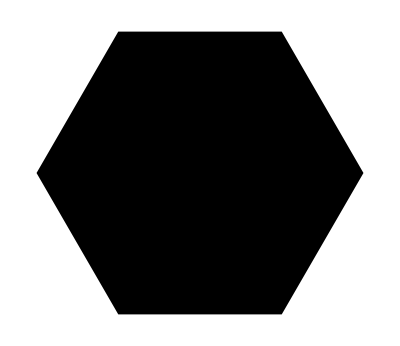

```mathematica
Table[{Cos[2π k/6],Sin[2π k/6]},{k,0,5}]
Graphics[Polygon[%]]
```

Pictures of polygons:

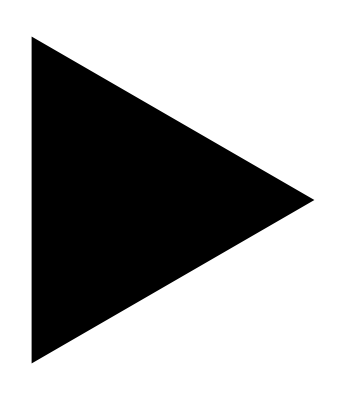
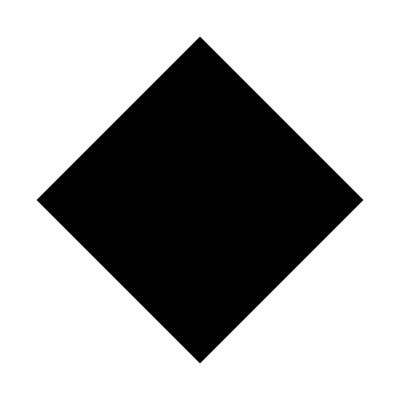
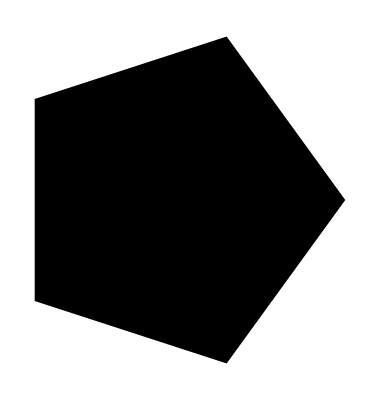
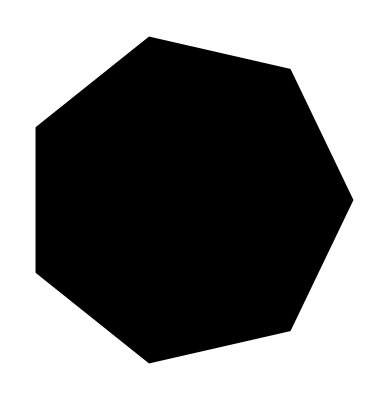
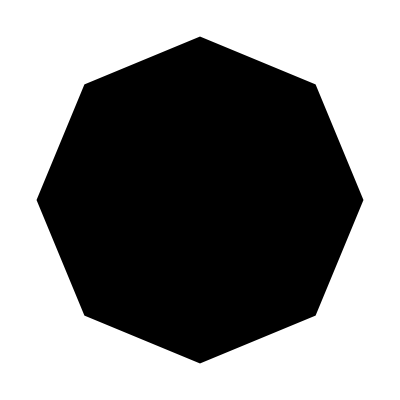
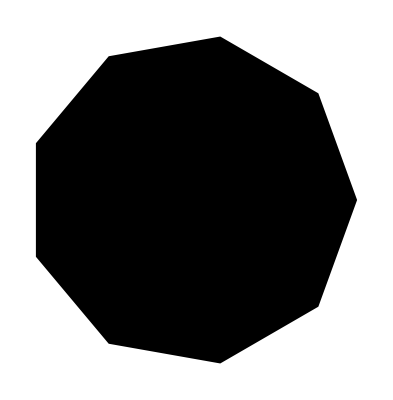
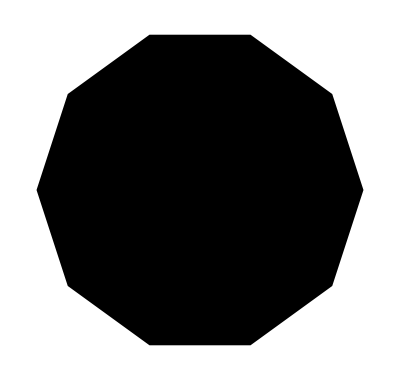
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Polygon[Table[{Cos[2π k/i],Sin[2π k/i]},{k,0,i-1}]]],{i,3,10}]
```

Colors:

```mathematica
Table[ColorData["Rainbow"][x],{x,0,1,.1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The Periodic Table of the Elements:

```mathematica
Table[ElementData[i,"Abbreviation"],{i,1,100}]
```

{H,He,Li,Be,B,C,N,O,F,Ne,Na,Mg,Al,Si,P,S,Cl,Ar,K,Ca,Sc,Ti,V,Cr,Mn,Fe,Co,Ni,Cu,Zn,Ga,Ge,As,Se,Br,Kr,Rb,Sr,Y,Zr,Nb,Mo,Tc,Ru,Rh,Pd,Ag,Cd,In,Sn,Sb,Te,I,Xe,Cs,Ba,La,Ce,Pr,Nd,Pm,Sm,Eu,Gd,Tb,Dy,Ho,Er,Tm,Yb,Lu,Hf,Ta,W,Re,Os,Ir,Pt,Au,Hg,Tl,Pb,Bi,Po,At,Rn,Fr,Ra,Ac,Th,Pa,U,Np,Pu,Am,Cm,Bk,Cf,Es,Fm}

## Comprehension Questions:

### 3. For each of the following Table commands, complete the following sub-questions. (a) BEFORE EVALUATING THE COMMAND, what list do you expect the command to give? Or do you expect an error? (b) Now, evaluate the command. Did it do what you expect it to do? (c) If not, figure out what went wrong with your reasoning.

```mathematica
Table[{s,7,9},{t,3,5}]
```

```mathematica
Table[{x,y},{x,2,4},{y,5,7}]
```

```mathematica
Table[xy,{x,2,4},{y,5,7}]
```

```mathematica
Table[Plot[x^n,{n,-2,2}],{x,1,10}]
```

```mathematica
Table[CountryData[country,"Population"],{country,{"France","United States","China"}}]
```

### 4. Create the table of possibilities of what happens when you roll two six-sided dice. What is their sum? What is their product? Evaluate and use these provided Table commands:

```mathematica
AddDice=Table[i+j,{i,1,6},{j,1,6}]
MultDice = Table[i*j,{i,1,6},{j,1,6}]
```

Does this do what you expect?  Now use TableForm to output AddDice and MultDice in a more readable format.

## Useful list commands

### Length

Length will tell you how many elements there are in the list.

```mathematica
Length[{1,2,3}]
```

3

```mathematica
Length[{1,{2,3}}]
```

2

### Total

Total will sum the values in the list.

```mathematica
Total[{1,2,3}]
```

6

```mathematica
powersOfTen=Table[10^i,{i,0,5}]
```

{1,10,100,1000,10000,100000}

```mathematica
Total[powersOfTen]
```

111111

### Flatten

When there are nested lists and you would like to remove some of the extra braces, you should use Flatten.

```mathematica
list=Table[x*y,{x,3},{y,3}]
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
Flatten[list]
```

{1,2,3,2,4,6,3,6,9}

You can also specify how many layers of braces you want to remove.

```mathematica
list2=Table[{x,y},{x,3},{y,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
Flatten[list2]
```

{1,1,1,2,1,3,2,1,2,2,2,3,3,1,3,2,3,3}

```mathematica
Flatten[list2,1]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

## Prepend and Append

When you want to add elements to the end of a preexisting list, use Append.  To add elements to the beginning, use Prepend.
This is often used in conjunction with redefining the preexisting list.

```mathematica
powersOfTen=Table[10^i,{i,0,5}]
```

{1,10,100,1000,10000,100000}

```mathematica
Append[powersOfTen,10^6]
```

{1,10,100,1000,10000,100000,1000000}

```mathematica
powersOfTen
```

{1,10,100,1000,10000,100000}

```mathematica
Prepend[powersOfTen,0]
```

{0,1,10,100,1000,10000,100000}

You can see that powersOfTen does not change when using Append or Prepend. 
You need to redefine powersOfTen if you want to actually add an entry to the list for future use.

```mathematica
powersOfTen=Append[powersOfTen,10^6]
```

{1,10,100,1000,10000,100000,1000000}

```mathematica
powersOfTen
```

{1,10,100,1000,10000,100000,1000000}

## Accessing parts of lists

It is often useful to single out one or more of the entries of a list.  For this we use double square brackets [[n]], (same as Part).

```mathematica
powersOfTen[[5]]
```

10000

```mathematica
Part[powersOfTen,5]
```

10000

When the list is a nested list, you can reference an entry (a sublist) or even an entry of the sublist.

```mathematica
nestedList={{1,2},{3,4},{5,6}};
```

```mathematica
nestedList[[2]]
```

{3,4}

```mathematica
nestedList[[2,1]]
```

3

## Comprehension Questions:

### 5. For each of the following commands, complete the following sub-questions. (a) What list do you expect the command to give? Or do you expect an error? (b) Now evaluate the command. Did it do what you expect it to do? (c) If not, figure out what went wrong with your reasoning.

```mathematica
Length[{1,2,3,4}]
```

```mathematica
Length[{{1,2,3}}]
```

```mathematica
Total[{1,2,3,4}]
```

```mathematica
Total[{{1,2},{3,4}}]
```

```mathematica
Total[{{1,2,3}}]
```

```mathematica
Flatten[{{{{1},2},3},4}]
```

```mathematica
Flatten[{{{{1},2},3},4},2]
```

```mathematica
Append[{1,2,3,4},{1}]
```

```mathematica
Append[{{1,2},{3,4}},5,6]
```

```mathematica
Append[{{1,2},{3,4}},{5,6}]
```

```mathematica
Part[powersOfTen,6]
```

```mathematica
Part[powersOfTen,{1,3,5}]
```

Discuss these answers with your neighbors.

### 6. Consider rolling two dice and taking the sum of the values. What is the average value for this sum? What is the average value for the product of two rolled dice? Three rolled dice? Four?

### 7. Here are two lists which represent the x- and y-coordinates of points, and an incorrect Table command that hopes to collect the points into a list of ordered x,y pairs. Figure out what is wrong with the command and fix it.

```mathematica
x={1,2,3,4,5}
y={2,5,10,17,26}
points=Table[{x[i],y[i]},{i,1,Length[x]}]
```

#### Solution:

You need to use double brackets to reference parts of a list.

```mathematica
points=Table[{x[[i]],y[[i]]},{i,1,Length[x]}]
```